## clear variable

```mathematica
Clear["Global`*"]
```

## set parameters

```mathematica
{α,β,µa1,µb1,µa2,µb2,T,allM1, allM2, c}={5,3,0.1,0.09,0.1,0.09,100,100,20,1.5}
```

{5,3,0.1,0.09,0.1,0.09,100,100,20,1.5}

## number of females emerging at time t : f(t)

### define f(t)

```mathematica
pdf[t_]=PDF[BetaDistribution[α,β],t]
```

Piecewise[{{105 (1-t)^2 t^4, 0<t<1}, {0, True}}]

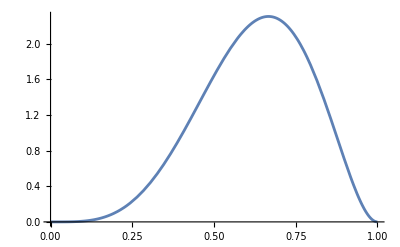

```mathematica
Plot[pdf[t]//Evaluate,{t,0,1}]
```

```mathematica
f[t_]=pdf[t]/.t->t/100
```

Piecewise[{{(21 (1-t/100)^2 t^4)/20000000, 0<t/100<1}, {0, True}}]

### plot f(t)

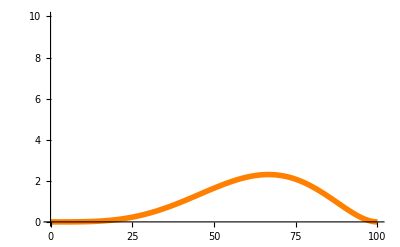

```mathematica
p0= Plot[f[t]//Evaluate,{t,0,T},
PlotRange->{{0,T},{0,10}},
PlotStyle->Directive[Orange,Thickness[0.01]]]
```

```mathematica
Integrate[f[t],{t,0,T}]
```

100

## number of females at time t : F(t)

### define F(t)

```mathematica
F[t_]=Integrate[f[x]*Exp[-µa1(t-x)],{x,0,t},Assumptions->0<t<T]
```

1.05×10^-9 ⅇ^(-0.1 t) (-5.52×10^9+5.52×10^9 ⅇ^(0.1 t)-5.52×10^8 ⅇ^(0.1 t) t+2.76×10^7 ⅇ^(0.1 t) t^2-920000. ⅇ^(0.1 t) t^3+23000. ⅇ^(0.1 t) t^4-260. ⅇ^(0.1 t) t^5+ⅇ^(0.1 t) t^6)

### plot F(t)

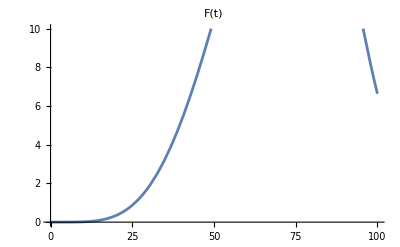

```mathematica
Plot[F[t],{t,0,T},
PlotRange->{{0,T},{0,10}},
PlotLabel->"F(t)"]
```

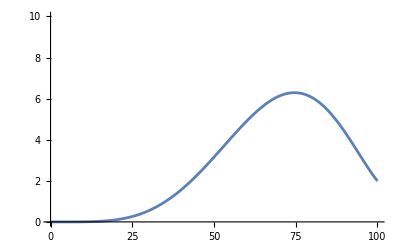

```mathematica
p00=Plot[0.3 F[t],{t,0,T},
PlotRange->{{0,T},{0,10}}]
```

## number of early male emerging at time t : g1(t) number of late male emerging at time t : g2(t) number of early male at time t : m1(t) number of late male at time t : m2(t)

### define g1(t)

```mathematica
g1[t_]=C1 Exp[-µa1 t]D[f[t]Exp[(µa1-µb1)t],t]
```

C1 ⅇ^(-0.1 t) (0.01 ⅇ^(0.01 t) (Piecewise[{{(21 (1-t/100)^2 t^4)/20000000, 0<t/100<1}, {0, True}}])+ⅇ^(0.01 t) (Piecewise[{{0, t<0||t==0}, {(21 (-100+t)^2 t^3)/50000000000+(21 (-100+t) t^4)/100000000000, 0<t<100}, {0, True}}]))

### define m1(t)

```mathematica
m1[t_]=Integrate[g1[x] Exp[-µa1(t-x)],{x, 0, t}, Assumptions->0<t<T]
```

1.05×10^-10 C1 ⅇ^(-0.09 t) (-100.+t)^2 t^4

### define g2(t)

```mathematica
(*g2[t_]=C2 Exp[-µa2 t]D[f[t]Exp[(µa2-µb2)t],t]-(1/c)m1[ts1]Exp[µa1 ts1]Exp[-µa2 t]D[Exp[(µa2-µa1)t], t]*)
```

```mathematica
g2[t_]=C2 Exp[-µa2 t]D[f[t]Exp[(µa2-µb2)t],t]-(1/c)(µa2-µa1) m1[ts1]Exp[(ts1-t)µa1]
```

0.+C2 ⅇ^(-0.1 t) (0.01 ⅇ^(0.01 t) (Piecewise[{{(21 (1-t/100)^2 t^4)/20000000, 0<t/100<1}, {0, True}}])+ⅇ^(0.01 t) (Piecewise[{{0, t<0||t==0}, {(21 (-100+t)^2 t^3)/50000000000+(21 (-100+t) t^4)/100000000000, 0<t<100}, {0, True}}]))

### define m2(t)

```mathematica
m2[t_] = Integrate[g2[x] Exp[-µa2(t-x)],{x, ts1, t},Assumptions->{0<t<T, 0<ts1<T}]
```

Piecewise[{{1.05×10^-10 C2 ⅇ^(-0.1 t) (10000. ⅇ^(0.01 t) t^4-200. ⅇ^(0.01 t) t^5+ⅇ^(0.01 t) t^6-10000. ⅇ^(0.01 ts1) ts1^4+200. ⅇ^(0.01 ts1) ts1^5-1. ⅇ^(0.01 ts1) ts1^6), (0.<t<100.&&t-1. ts1>0.&&ts1>0.)||(0.<t<100.&&t-1. ts1<0.&&ts1<100.)}, {0., True}}]

### equation1（The total number of early male equal allM1）

```mathematica
eq1=Integrate[g1[x],{x,0,ts1},Assumptions->{0<t<T,0<ts1<T}]==allM1
```

1.97576×10^-16 C1 ⅇ^(-0.09 ts1) (-5.6×10^14+5.6×10^14 ⅇ^(0.09 ts1)-5.04×10^13 ts1-2.268×10^12 ts1^2-6.804×10^10 ts1^3+3.78351×10^9 ts1^4-2.75562×10^7 ts1^5-59049. ts1^6)==100

### equation2（The total number of late male equal allM2）

```mathematica
(*負の値を0に変換するBoole関数を作成*)
```

```mathematica
nonNegativeBoole[x_]:=Boole[x>=0];
```

```mathematica
eq2 = Integrate[g2[x]*nonNegativeBoole[g2[x]], {x, ts1, T},Assumptions->{0<t<T,0<ts1<T}] == allM2
```

(Piecewise[{{-0.000934774 C2, ts1≤70.1562&&C2<0.}, {-1.97576×10^-16 C2 ⅇ^(-9.-0.09 ts1) (-4.53773×10^18+5.258×10^16 ⅇ^(0.09 ts1)-4.08395×10^17 ts1-1.83778×10^16 ts1^2-5.51334×10^14 ts1^3+3.06581×10^13 ts1^4-2.2329×10^11 ts1^5-4.78479×10^8 ts1^6), C2==0.||(C2≤0.&&ts1>70.1562)}, {-1.97576×10^-16 C2 ⅇ^(-28.8141-0.09 ts1) (-1.82799×10^27+9.70733×10^14 ⅇ^(22.5+0.09 ts1)-1.6452×10^26 ts1-7.40338×10^24 ts1^2-2.22101×10^23 ts1^3+1.23504×10^22 ts1^4-8.9951×10^19 ts1^5-1.92752×10^17 ts1^6), C2>0.&&ts1<70.1562}, {0., True}}])==20

### equation3（Late male and early male fitness are equal）

```mathematica
eq3 = 1/((µa1-µb1)C1)==1/((µa2-µb2)C2)
```

100./C1==100./C2

### find ts1, C1 and C2

```mathematica
(*NSolve[{eq1,eq22,eq3},{ts1,C1,C2}]*)
```

```mathematica
sol = FindRoot[{eq1, eq2, eq3},{{ts1,45},{C1, 1000},{C2, 1000}}]
```

{ts1→41.2987,C1→1087.99,C2→1087.99}

```mathematica
(*NSolve[{eq1,eq22,eq3},{ts1,C1,C2}]*)
```

### plot g1(t), g2(t)

```mathematica
p1=Plot[g1[t]/. sol,{t,0,ts1/.sol},
PlotRange->{{0,T},{-2,10}},
PlotStyle->Directive[Blue,Thickness[0.01]]];
```

```mathematica
p2=Plot[g2[t]/. sol,{t,ts1/.sol,T},
PlotRange->{{0,T},{-2,10}},
PlotStyle->Directive[RGBColor[0.0039,0.8078,0.8196],Thickness[0.01]]];
```

```mathematica
(*Show[p1,p2,
PlotLabel->"g(t)"]*)
```

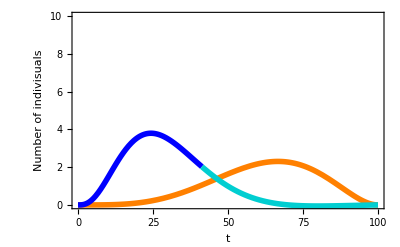

```mathematica
fig1=Show[p0, p1, p2,
Frame->True,
FrameLabel->{Style["t",　FontSize->15], Style["Number of indivisuals",　FontSize->15]},
FrameStyle->Directive[Black,AbsoluteThickness[1.3]],
Axes->False]
```

```mathematica
Integrate[g1[t]/. sol,{t,0,ts1/.sol}]
```

100.

```mathematica
Integrate[g2[t]/. sol,{t,ts1/.sol,T}]
```

18.983

### plot m1(t), m2(t)

```mathematica
p3=Plot[0.3*m1[t]/. sol,{t,0,ts1/.sol},
PlotRange->{{0,T},{0,10}},
PlotStyle->Directive[Red,Thickness[0.01]]];
```

```mathematica
p4=Plot[0.3*m1[ts1]Exp[-µa1(t-ts1)]/. sol,{t,ts1/.sol,T},
PlotRange->{{0,T},{0,10}},
PlotStyle->Directive[Red,Thickness[0.01]]];
```

```mathematica
p5=Plot[0.3*m2[t]/. sol,{t,ts1/.sol,T},
PlotRange->{{0,T},{0,10}},
PlotStyle->Directive[RGBColor[1,0.7529,0.7961],Thickness[0.01]]];
```

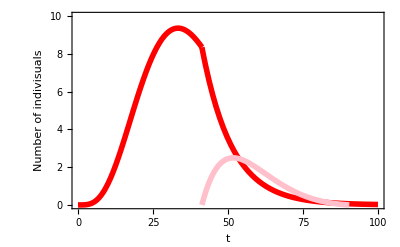

```mathematica
fig2=Show[p3,p4,p5,
Frame->True,
FrameLabel->{Style["t",FontSize->15],Style["Number of indivisuals",FontSize->15]},
FrameStyle->Directive[Black,AbsoluteThickness[1.3]],
Axes->False]
```